```mathematica
MultinormalDistribution[{{1,0,0},{0,1,0},{0,0,1}}]
```

MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}]

```mathematica
PDF[MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}],{x,y,z}]
```

(ⅇ^(1/2 (-x^2-y^2-z^2)))/(2 √2 π^(3/2))

```mathematica
v=RandomVariate[MultinormalDistribution[{{1,0,0},{0,1,0},{0,0,1}}],10^5]
```

```mathematica
data=v[[;;,1]]
```

```mathematica
Variance[data]
```

1.0042

```mathematica
getData[num_,sigmax_,sigmay_,sigmaz_]:=RandomVariate[MultinormalDistribution[{{sigmax,0,0},{0,sigmay,0},{0,0,sigmaz}}],num];
ℋ[data_]:=DistributionFitTest[data,Automatic,"HypothesisTestData"];
showData[data_]:=Show[Histogram[data,Automatic,"ProbabilityDensity"],Plot[PDF[ℋ[data]["FittedDistribution"],x],{x,-5,5},PlotStyle->Thick]];
countVar1D[data_]:=Variance[data[[;;,1]]];
```

```mathematica
data=getData[10^6,1.5,2.,0.9];

countVar1D[data]
```

1.50084

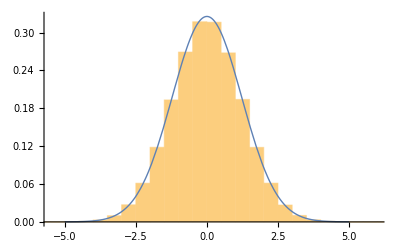

```mathematica
showData[data[[;;,1]]]
```

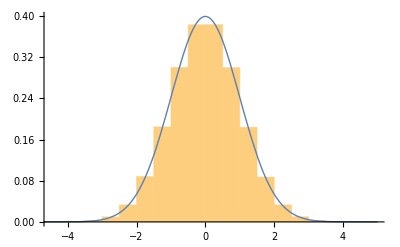

```mathematica
showData[data[[;;,1]]]
```

```mathematica
Norm[{{2,0,0},{0,2,0},{0,0,2}}]
```

2